# (stabilizerstates.wl) Instructions for Use

Included within are instructions for use and examples pertaining to the Mathematica package stabilizerstates.wl.

```mathematica
(*Package can be downloaded from https://github.com/WMunizzi/StabilizerStateData/blob/main/stabilizerstates.wl and imported to Mathematica notebook from whichever external storage it is located in.*)
<<"/Applications/Mathematica.app/Contents/AddOns/Packages/stabilizerstates.wl"
```

## Examples of General Functions

```mathematica
(*The Swap function is used internally within certain functions to swap elements of a list. The example below swaps elements at indices 1 and 3 in OrderedList.*)

OrderedList = {1,2,3,4,5};
Swap[OrderedList,1,3]
```

{3,2,1,4,5}

```mathematica
(*The PermutedIdentity function gives the 2^n x 2^n permutation matrix that reorders a density matrix of n qubits into the new ordering requested. The example below replaces the natural ordering 1,2,3 with the ordering 2,3,1.*)

NewOrdering = {2,3,1};
dimension = 3;
PermutedIdentity[dimension,NewOrdering]
```

{{1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1}}

## Examples of Quantum Entropy Functions

```mathematica
(*The DensityMatrix function gives the density matrix corresponding to the input ket.*)
twoqubitsampleket = {{1},{0},{0},{1}};
DensityMatrix[twoqubitsampleket]
```

{{1,0,0,1},{0,0,0,0},{0,0,0,0},{1,0,0,1}}

```mathematica
(*The KetProjector function projects out a density matrix into the ket representation of the measurement basis.*)
sampledensity = {{1,0,0,1},{0,0,0,0},{0,0,0,0},{1,0,0,1}};
KetProjector[sampledensity]
```

{{1},{0},{0},{1}}

```mathematica
(*The TraceSystem function gives the reduced density matrix of a subsystem of qubits, after tracing out over undesired qubits. For example, we can trace out qubit 1 to give the reduced density matrix for qubit 2,*)
TraceSystem[sampledensity,{1}]
```

{{1,0},{0,1}}

```mathematica
(*Similarly, computing the reduced density matrix of qubits 1 and 2 by tracing out the third qubit in a 3-qubit system,*)
threequbitsampleket = {{1},{0},{0},{0},{0},{0},{0},{1}};
threequbitsampledensity = DensityMatrix[threequbitsampleket];

TraceSystem[threequbitsampledensity,{3}]
```

{{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1}}

```mathematica
(*The SvonNeumannBinary function computes the entanglement entropy for a chosen subsystem of qubits in an n-qubit system. The overall system is input as a state ket. For example, computing the entanglement entropy of the third qubit in a 3-qubit system,*)
SvonNeumannBinary[threequbitsampleket,{1}]
```

1

```mathematica
(*The EntropyVectorBuilder function computes the vonNeumann entropy for all subsytems in an n-qubit system, and orders the set of entanglement entropies into a vector of length 2^n-1. The order of this vector follows the natural ordering, e.g. (Subscript[S, A],Subscript[S, B],Subscript[S, C],Subscript[S, AB],Subscript[S, AC],Subscript[S, BC],Subscript[S, ABC]) for a 3-qubit system.*)
threequbitvacuumket = {{1},{0},{0},{0},{0},{0},{0},{0}};
threequbitGHZket = {{1},{0},{0},{0},{0},{0},{0},{1}};

EntropyVectorBuilder[threequbitvacuumket]
EntropyVectorBuilder[threequbitGHZket]
```

{{0},{0},{0},{0},{0},{0},{0}}

{{1},{1},{1},{1},{1},{1},{0}}

```mathematica
(*The ReducedEntropyVectorBuilder function computes the entropy vector for a chosen state, then reduces the entropy vector according to purity constraints. For a pure system, the entanglement entropy of the full system is 0, therefore the last component of the entropy vector will always be 0. Furthermore, the entanglement entropy of any subregion will be equal to the entanglement entropy of its complement subregion, since one purifies the other. Therefore, an entropy vector of length 2^n-1 can be reduced to one of length 2^(n-1)-1 if the overall system is pure.*)
ReducedEntropyVectorBuilder[threequbitvacuumket]
ReducedEntropyVectorBuilder[threequbitGHZket]
```

{{0},{0},{0}}

{{1},{1},{1}}

## Examples of Quantum Logic Gates

```mathematica
(*The HadamardAction, PhaseAction, and CNOTAction functions give the matrices that act on a state when a Hadamard, Phase, or CNOT gate is applied respectively.*)

(*For example, the matrix corresponding to a Hadamard gate acting on the first qubit of a 2-qubit system is given by,*)
dim = 2;
HadamardAction[2,1]
```

{{1,1,0,0},{1,-1,0,0},{0,0,1,1},{0,0,1,-1}}

```mathematica
(*Similarly, a phase gate applied to the second qubit in a 4-qubit system is described by the matrix,*)
dim = 4;
PhaseAction[4,2]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ}}

```mathematica
(*A CNOT gate acts on any two qubits in an n-qubit system. For example, the matrix corresponding to the 3-qubit CNOT gate with the first qubit the control, and second qubit the target is, *)
dim = 3;
CNOTAction[3,{1,2}]
```

{{1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0}}

```mathematica
(*Or with the third qubit the control, and the first qubit the target,*)
dim = 3;
CNOTAction[3,{3,1}]
```

{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}

## Examples of Quantum Circuits

## Examples of Stabilizer State Functions

```mathematica
twoqubitstabilizerstates = StabilizerStateSetGenerator[2];
```

3

7

15

29

43

55

60

```mathematica
twoqubitstatemap = StabilizerStateMap[twoqubitstabilizerstates]
```

Gates Compiled.

{{{{1},{1},{0},{0}},{H,{1}},{{1},{0},{0},{0}},{{0}}},{{{1},{0},{1},{0}},{H,{2}},{{1},{0},{0},{0}},{{0}}},{{{1},{0},{0},{0}},{P,{1}},{{1},{0},{0},{0}},{{0}}},{{{1},{0},{0},{0}},{P,{2}},{{1},{0},{0},{0}},{{0}}},{{{1},{0},{0},{0}},{CNOT,{1,2}},{{1},{0},{0},{0}},{{0}}},351,{{{0},{1},{ⅈ},{0}},{P,{1}},{{0},{1},{-1},{0}},{{1}}},{{{0},{1},{-ⅈ},{0}},{P,{2}},{{0},{1},{-1},{0}},{{1}}},{{{0},{0},{1},{-1}},{CNOT,{1,2}},{{0},{1},{-1},{0}},{{0}}},{{{0},{1},{0},{-1}},{CNOT,{2,1}},{{0},{1},{-1},{0}},{{0}}}}
 |  |  |  |

```mathematica
twoqubitreducedentropyvectors = ReducedEntropyVectors[twoqubitstabilizerstates];
```

## Examples of Visualization Functions

## Graph Builders

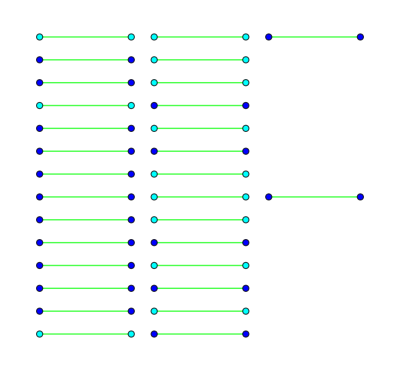

```mathematica
(*The ReachabilityGraphBuilder function is used to generate graphs from a map of stabilizer states.*)

desiredGates1= {{"H",{1}}};

ReachabilityGraphBuilder[twoqubitstatemap,desiredGates1,twoqubitreducedentropyvectors,False,False,Automatic]
```

```mathematica
desiredGates2= {{"H",{1}},{"H",{2}},{"CNOT",{1,2}},{"CNOT",{2,1}}};

ReachabilityGraphBuilder[twoqubitstatemap,desiredGates2,twoqubitreducedentropyvectors,False,False,Automatic]
```

-Graphics-